```mathematica
FiveFirst[a_,b_]:=Block[{},
If[a<5,
If[b<5,
b-a,
-1
],
If[b<5,
1,
b-a
]
]
]
```

```mathematica
Sort[{1,2,3,4,5,6,7},FiveFirst]
```

{5,6,7,1,2,3,4}

```mathematica
ZykovDecomposition2[g_Graph,vertices_List]:=Block[{split,left, right,left2,right2,middle2,middle,sols,lefta,middlea,righta},
If[Length[vertices]==0,Print[g];Throw[{"Cannot decompose with empty vertex list ",g}]];
split= ConnectedComponents[VertexDelete[g,vertices]];
If[Length[split]!=2,Print[vertices];Return[ZykovDecomposition2[g,Rest[vertices]]]];
left=VertexDelete[g,split[[1]]];
right=VertexDelete[g,split[[2]]];
middle=VertexDelete[g,Select[DeleteDuplicates[Join[VertexList[left],VertexList[right]]],!MemberQ[vertices,#]&]];
left2=MakeComplete[left,vertices];
right2=MakeComplete[right,vertices];
middle2=MakeComplete[middle,vertices];
sols=Reverse[Map[SymbolToSets,Sort[FindFullFormula[middle],CompareSymbols]]];
Total[
Table[
middlea=ApplyToGraph[middle2,sol];
lefta=Graph[ApplyToGraph[left2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
righta=Graph[ApplyToGraph[right2,sol],GraphHighlight->EdgeList[middlea],GraphHighlightStyle->"Thick",ImageSize->200];
(Framed[AutoZykov[righta]]*Framed[AutoZykov[lefta]])/AutoZykov[middlea],
{sol,sols}
]
]
]
```

```mathematica
AutoZykov[g_]:=Block[{pivotVertex},
If [CompleteGraphQ[g],
Product[(x-k),{k,VertexCount[g]-1}]
,
If[VertexCount[g]<=7,
ChromaticPolynomial[g,x],
(* choose a vertex *)
pivotVertex=First[Sort[Table[{k,VertexDegree[g,k]},{k,VertexList[g]}],FiveFirst[#1[[2]],#2[[2]]]&]][[1]];
ZykovDecomposition2[g,Map[First,First[FindHamiltonianCycle[ VertexDelete[NeighborhoodGraph[g,pivotVertex],pivotVertex]]]]]
]
]
]
```

```mathematica
With[{g=Graph[ReadGrof[3],VertexLabels->"Name"]},First[Sort[Table[{k,VertexDegree[g,k]},{k,VertexList[g]}],FiveFirst[#1[[2]],#2[[2]]]&]]]
```

{3,5}

```mathematica
With[{g=Graph[ReadGrof[3],VertexLabels->"Name"]},Map[First,First[FindHamiltonianCycle[ VertexDelete[NeighborhoodGraph[g,3],3]]]]]
```

{1,2,6,4,5}

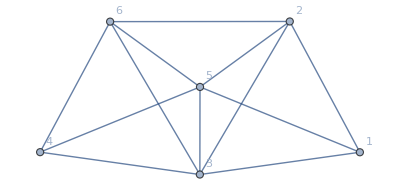
```mathematica
ConnectedComponents[VertexDelete[-Graphics-,{6,4,5}]]
```

{{1,2,3}}

```mathematica
Product[(x-k),{k,VertexCount[CompleteGraph[6]]-1}]//Expand
```

-120+274 x-225 x^2+85 x^3-15 x^4+x^5

```mathematica
ChromaticPolynomial[CompleteGraph[6],x]//Factor
```

(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x

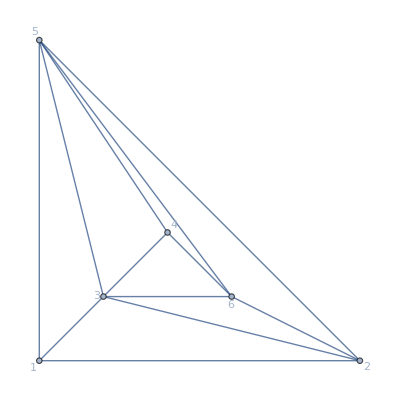

```mathematica
Graph[ReadGrof[3],VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```

```mathematica
Factor[ChromaticPolynomial[ReadGrof[3],x]]
```

(-3+x)^3 (-2+x) (-1+x) x

```mathematica
Length [Factor[ChromaticPolynomial[ReadGrof[3],x]]]
```

4

```mathematica
Table[k,{k,Factor[ChromaticPolynomial[ReadGrof[3],x]]}]
```

Table::iterb: Iterator {k,(-3+x)^3 (-2+x) (-1+x) x} does not have appropriate bounds.

Table[k,{k,(-3+x)^3 (-2+x) (-1+x) x}]

```mathematica
Table[With[{chrom=Factor[ChromaticPolynomial[ReadGrof[w],x]]},Table[chrom[[k]],{k,Length[chrom]}]],{w,10,10000,200}]//Flatten//DeleteDuplicates
```

{(-3+x)^5,-2+x,-1+x,x,(-3+x)^2,-332+498 x-303 x^2+94 x^3-15 x^4+x^5,(-3+x)^4,119-133 x+58 x^2-12 x^3+x^4,-35+30 x-9 x^2+x^3,-32+29 x-9 x^2+x^3,(-3+x)^8,(-3+x)^6,(-3+x)^9,-383+542 x-315 x^2+95 x^3-15 x^4+x^5,(-3+x)^3,1454-2330 x+1608 x^2-619 x^3+141 x^4-18 x^5+x^6,1385-2265 x+1588 x^2-617 x^3+141 x^4-18 x^5+x^6,-3962+7978 x-6986 x^2+3458 x^3-1049 x^4+196 x^5-21 x^6+x^7,-3+x,1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6,-398+553 x-317 x^2+95 x^3-15 x^4+x^5,-447+591 x-327 x^2+96 x^3-15 x^4+x^5,(-32+29 x-9 x^2+x^3)^2,(-3+x)^7,(-3+x)^10}

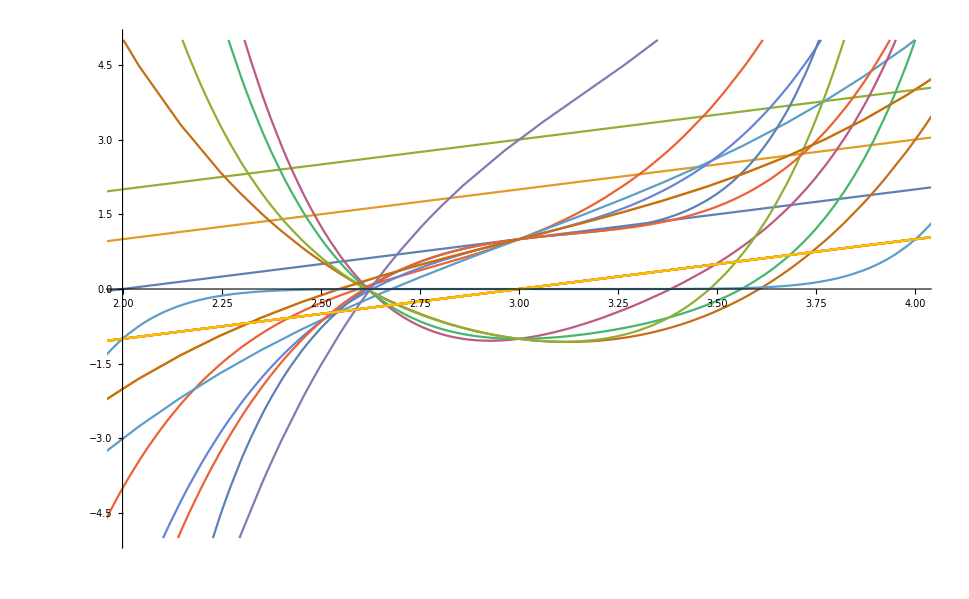

```mathematica
Plot[{-2+x,-1+x,x,-332+498 x-303 x^2+94 x^3-15 x^4+x^5,(-3+x),119-133 x+58 x^2-12 x^3+x^4,-35+30 x-9 x^2+x^3,-32+29 x-9 x^2+x^3,(-3+x),(-3+x),(-3+x),-383+542 x-315 x^2+95 x^3-15 x^4+x^5,(-3+x),1454-2330 x+1608 x^2-619 x^3+141 x^4-18 x^5+x^6,1385-2265 x+1588 x^2-617 x^3+141 x^4-18 x^5+x^6,-3962+7978 x-6986 x^2+3458 x^3-1049 x^4+196 x^5-21 x^6+x^7,-3+x,1199-2077 x+1525 x^2-610 x^3+141 x^4-18 x^5+x^6,-398+553 x-317 x^2+95 x^3-15 x^4+x^5,-447+591 x-327 x^2+96 x^3-15 x^4+x^5,(-32+29 x-9 x^2+x^3),(-3+x)^7,(-3+x)},{x,0,5}, PlotRange->{{2,4},{-5,5}}]
```

```mathematica
With[{chrom=Factor[ChromaticPolynomial[ReadGrof[1],x]]},Plot[Table[Function[x,chrom[[k]]][x],{k,Length[chrom]}],{x,0,5}]]
```

-Graphics-

```mathematica
AutoZykov[ReadGrof[1000]]
```

((-3+x) (-2+x) (-1+x) 162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7)/((-2+x) (-1+x))+(7 (-4+x) (-3+x) (-2+x) (-1+x) ((-3+x) (-2+x) (-1+x) 18 x-39 x^2+29 x^3-9 x^4+x^5)/((-2+x) (-1+x))+(3 (-4+x) (-3+x) (-2+x) (-1+x) -54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)/((-3+x) (-2+x) (-1+x))+((-5+x) (-4+x) (-3+x) (-2+x) (-1+x) 216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)/((-4+x) (-3+x) (-2+x) (-1+x)))/((-3+x) (-2+x) (-1+x))+(6 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) (4 (-4+x) (-3+x) (-2+x) (-1+x) -54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)/((-3+x) (-2+x) (-1+x))+(5 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) 216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)/((-4+x) (-3+x) (-2+x) (-1+x))+((-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) ((-5+x) (-4+x) (-3+x) (-2+x) (-1+x) 216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)/((-4+x) (-3+x) (-2+x) (-1+x)))/((-5+x) (-4+x) (-3+x) (-2+x) (-1+x)))/((-4+x) (-3+x) (-2+x) (-1+x))+((-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) ((-5+x) (-4+x) (-3+x) (-2+x) (-1+x) (4 (-4+x) (-3+x) (-2+x) (-1+x) -54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)/((-3+x) (-2+x) (-1+x))+(5 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) 216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)/((-4+x) (-3+x) (-2+x) (-1+x))+((-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) ((-5+x) (-4+x) (-3+x) (-2+x) (-1+x) 216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)/((-4+x) (-3+x) (-2+x) (-1+x)))/((-5+x) (-4+x) (-3+x) (-2+x) (-1+x)))/((-4+x) (-3+x) (-2+x) (-1+x)))/((-5+x) (-4+x) (-3+x) (-2+x) (-1+x))

First::nofirst: {} has zero length and no first element.

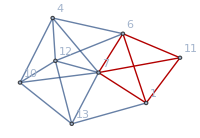

{13,7,5,10,4,8,1}

{7,5,10,4,8,1}

{5,10,4,8,1}

{10,4,8,1}

{4,8,1}

{8,1}

{1}

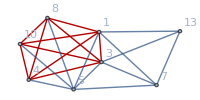

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

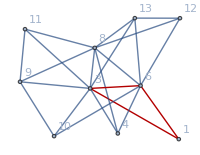

{1,3,9,6,10,5,7}

{3,9,6,10,5,7}

{9,6,10,5,7}

{6,10,5,7}

{10,5,7}

{5,7}

{7}

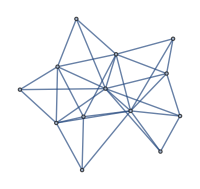

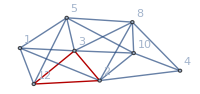

{4,13,12,1,14,5,6}

{13,12,1,14,5,6}

{12,1,14,5,6}

{1,14,5,6}

{14,5,6}

{5,6}

{6}

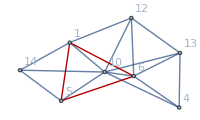

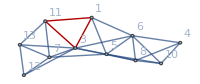

{1,7,5,8,6,12,2}

{7,5,8,6,12,2}

{5,8,6,12,2}

{8,6,12,2}

{6,12,2}

{12,2}

{2}

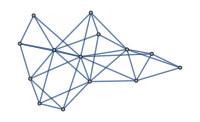

{7,14,3,8,10,13,6,1}

{14,3,8,10,13,6,1}

{3,8,10,13,6,1}

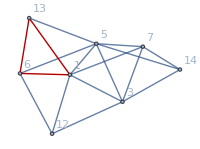

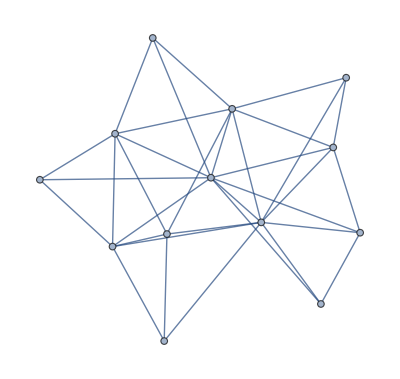
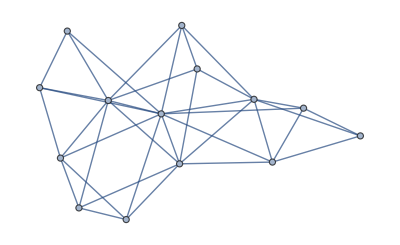
{{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-},{Cannot decompose with empty vertex list ,-Graphics-}}

```mathematica
Table[Catch[AutoZykov[ReadGrof[k]]],{k,20000,100000,10000}]
```

```mathematica
ChromaticPolynomial[ReadGrof[1000],x]
```

13122 x-54675 x^2+99873 x^3-105948 x^4+72576 x^5-33642 x^6+10710 x^7-2316 x^8+326 x^9-27 x^10+x^11

```mathematica
Expand[(-3+x) (162 x-459 x^2+513 x^3-294 x^4+92 x^5-15 x^6+x^7)+7 (-4+x) ((-3+x) (18 x-39 x^2+29 x^3-9 x^4+x^5)+3 (-4+x) (-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)+(-5+x) (216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7))+6 (-5+x) (4 (-4+x) (-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)+5 (-5+x) (216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)+(-6+x) (-5+x) (216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7))+(-6+x) (-5+x) (4 (-4+x) (-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6)+5 (-5+x) (216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7)+(-6+x) (-5+x) (216 x-594 x^2+639 x^3-350 x^4+104 x^5-16 x^6+x^7))]
```

13122 x-54675 x^2+99873 x^3-105948 x^4+72576 x^5-33642 x^6+10710 x^7-2316 x^8+326 x^9-27 x^10+x^11

```mathematica
Sort[Table[{k,VertexDegree[g,k]},{k,VertexList[g]}],FiveFirst[#1[[2]],#2[[2]]]&]
```

{{8,5},{2,6},{5,6},{6,6},{3,7},{1,3},{4,3},{7,4},{10,4},{9,4}}

```mathematica
AutoZykov[g]
```

8

```mathematica
VertexDelete[NeighborhoodGraph[g,8],8]
```

-Graphics-

```mathematica
First[FindHamiltonianCycle[ VertexDelete[NeighborhoodGraph[g,8],8]]]
```

{3<->9,9<->6,6<->4,4<->5,5<->3}

```mathematica
Map[First,First[FindHamiltonianCycle[ VertexDelete[NeighborhoodGraph[g,8],8]]]]
```

{3,9,6,4,5}

```mathematica
VertexDegree
```

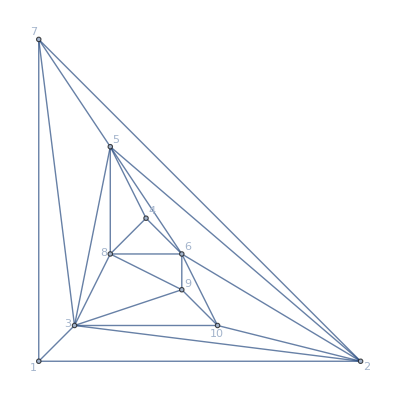

```mathematica
g=Graph[ReadGrof[100], VertexLabels->"Name", GraphLayout->"PlanarEmbedding"]
```